```mathematica
SetDirectory["/Users/arsenytokarev/Desktop/BMSTU_Practices/TSP/TSPXcode/TSPXcode/Helpers"];
```

```mathematica
coordOfCountries = {
{21,23 },
{13, -43},
{43, -4},
{-10, -12},
{-15, -95},
{26, 63},
{-3, -80},
{61, 30}
};
```

```mathematica
coordOfCountries // MatrixForm
```

(21 | 23
13 | -43
43 | -4
-10 | -12
-15 | -95
26 | 63
-3 | -80
61 | 30)

## Calculating all costs from one point to another

```mathematica
costMatrix = DistanceMatrix[coordOfCountries] ;
costMatrix // MatrixForm // N
```

(0. | 66.4831 | 34.8281 | 46.7547 | 123.369 | 40.3113 | 105.759 | 40.6079
66.4831 | 0. | 49.2037 | 38.6005 | 59.0593 | 106.794 | 40.3113 | 87.367
34.8281 | 49.2037 | 0. | 53.6004 | 107.912 | 69.1231 | 88.8369 | 38.4708
46.7547 | 38.6005 | 53.6004 | 0. | 83.1505 | 83.1925 | 68.3593 | 82.4924
123.369 | 59.0593 | 107.912 | 83.1505 | 0. | 163.233 | 19.2094 | 146.291
40.3113 | 106.794 | 69.1231 | 83.1925 | 163.233 | 0. | 145.911 | 48.1041
105.759 | 40.3113 | 88.8369 | 68.3593 | 19.2094 | 145.911 | 0. | 127.264
40.6079 | 87.367 | 38.4708 | 82.4924 | 146.291 | 48.1041 | 127.264 | 0.)

```mathematica
(*Export["costMatrix.txt",N@costMatrix,"Table","FieldSeparators"->" "];*)
```

```mathematica
trip = Range[Length@coordOfCountries];
```

## Sketching route

```mathematica
Distance[tour_, i_, j_] := costMatrix[[  tour[[i]], tour[[j]]  ]];
```

```mathematica
Route[trip_] := Module[{points, lines, text}, 
points = Point[coordOfCountries];
text = Table[Text[Style[ToString@i, Medium,18, Blue], Offset[{ If[coordOfCountries[[i,1]] > 0, 10, -10], If[coordOfCountries[[i,2]] > 0, 10, -10]}, {coordOfCountries[[i, 1]], coordOfCountries[[i, 2]]}]], {i, 1, Length@coordOfCountries}];

lines =Arrow /@ Join[Table[{coordOfCountries[[  trip[[i]]  ]], coordOfCountries[[  trip[[i+1]]  ]]},{i, 1, Length@coordOfCountries - 1}], {{ coordOfCountries[[  trip[[Length@trip]]  ]], coordOfCountries[[  trip[[1]]  ]]}} ] ;
Print["Total route cost = ",N@Total@Join[Table[costMatrix[[  trip[[i]], trip[[i+1]]  ]],{i, 1, Length@trip - 1}], { costMatrix[[  trip[[Length@trip]], trip[[1]]  ]]} ]];
Graphics[{lines, points, text}]
];
```

Total route cost = 729.453

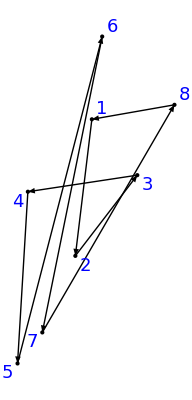

```mathematica
Route[trip]
```

```mathematica
NN[initTour_]:= Module[
{bestTour = initTour,
minRouteCost,
nextRouteIndex,
temp
},
For[i = 1, i < Length@bestTour , i++ ,
minRouteCost = +∞; 
nextRouteIndex = 0;
For[j = i+1, j≤ Length@bestTour, j++,
If[Distance[bestTour, i, j] < minRouteCost, 
minRouteCost = Distance[bestTour, i, j];
nextRouteIndex = j;
];
];
temp = bestTour[[i+1]];
bestTour[[i+1]] = bestTour[[nextRouteIndex]];
bestTour[[nextRouteIndex]] = temp;
];
bestTour
];
```

Total route cost = 426.086

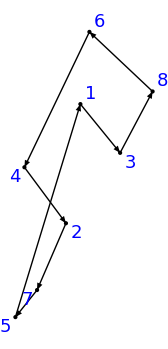

```mathematica
Route[NN[trip]]
```

```mathematica
TwoOpt[initTour_]:= Module[
{bestTour = {initTour, initTour[[1]]} // Flatten,
isImproved = True,
temp,
oldDelta, newDelta
},
While[isImproved,
isImproved = False;
For[i = 2, i < Length@bestTour - 1, i++, 
For[j = i+ 1, j ≤  Length@bestTour - 1, j++,
oldDelta = Distance[bestTour, i - 1,i] + Distance[bestTour, j, j+1];
newDelta = Distance[bestTour, i-1, j] + Distance[bestTour, i, j+1];
If[newDelta < oldDelta, 
isImproved = True;
bestTour = Join[ bestTour[[1;;i-1]], Join[  Reverse@bestTour[[i;;j]], bestTour[[j+1;;Length@bestTour]]  ] ]
];
];
];
];
bestTour[[1;;Length@bestTour - 1]]
]
```

Total route cost = 365.516

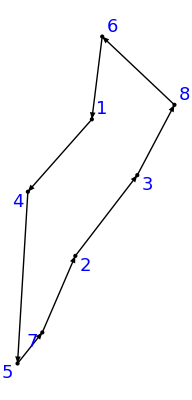

```mathematica
TwoOpt[trip] // Route
```